### Константы

```mathematica
If[True,
A            =- 0.024 ;
B            = 1.69 ;
CC          = 0.5 ;
α            = 10^-5                 (* K^-1 *);
Subscript[T, 0]          = 300                  (* K *);
Subscript[T, avg]       = 300                  (* K *);
Young   = 1.75 * 10^11  (* Па *);
σf          = 1.1 * 10^8      (* Па *);
ϵf          = 0.000628571 ;
l            = 10                     (* Длина стержня *);
Subscript[T, f]          =22                      (* Конечный момент времени *); 
Subscript[h, t]            = 0.05               (* Шаг времени *);
a            = 50                     (* Просто константа *);
n            =  4                    (* Число узлов сетки *);
Subscript[h, x]                                          (* Шаг сетки *);
];
```

### Определение функций распределения температуры в пространстве и времени

```mathematica
F[x_] := a Sin[(π x)/l];
Subscript[T, 1][x_, t_] := Subscript[T, avg] + F[x]t Sin[t];
Subscript[T, 2][ x_, t_ ] := Subscript[T, avg] + F[x] Cos[π t^2](t+1);
TT = Subscript[T, 1];
```

Тепловые деформации

```mathematica
Subscript[ϵ, t] [x_,tt_] := α(TT[x, tt] - Subscript[T, 0]);
```

```mathematica
Subscript[u, analytical] = 
First[Flatten[
DSolve[{
D[D[u[x,t], {x, 1}]-Subscript[ϵ, t][x, t], {x, 1}]== 0,
u[0, t] == 0, 
u[l, t] == 0
},u[x,t],{x, t}]]
]⟦2⟧  // FullSimplify
```

-(t (-5+x+5 Cos[(π x)/10]) Sin[t])/(1000 π)

### Численное решение (метод конечных разностей)

Проверки для шага и количества точек (можем выставлять и то, и то)

```mathematica
If[NumberQ[n],
Subscript[h, x] = l/n, 
If[NumberQ[Subscript[h, x]],n = IntegerPart[l/Subscript[h, x]]; Subscript[h, x] = l/n]
];
```

Создаем массив точек и значений функции f в них, далее решаем СЛАУ: Au = F(f(x_1), ..., f(x_n) ).

```mathematica
ϵf
```

0.000628571

```mathematica
points = Table[i*Subscript[h, x], {i, 0, n}];
```

```mathematica
στ = Table[0,{i, 0, n}];                                     (* значения напряжений во временном слое τ *)
σfv = Table[σf,{i, 0, n}];                                (* значения переменных пределов прочности *)
ϵτ = Table[0,{i, 0, n}];                                            (* значения полных деформаций во временном слое τ *)
ϵe = Table[0,{i, 0, n}];                                     (* значения упругих деформаций во временном слое τ *)
ϵT = Table[0,{i, 0, n}];                                            (* значения температурных деформаций во врменном слое τ *) 
ϵcrk = Table[0,{i, 0, n}];                                        (* значения деформаций за счет трещин *) 
Tτ = Table[0,{i, 0, n}];                                            (* значения температуры во временном слое τ *) 
Subscript[balance, normal] [x_, k_]:= Young x;                             (* функция, подставляемая в условие равновесия при напряжениях, меньших предельных *) 
Subscript[balance, crack][x_, k_]:=  σfv⟦k⟧(A + B ⅇ^(-CC x/ϵf));   (* функция, подставляемая в условие равновесия при напряжениях, больших предельных *) 
balances =  Table[0,{i, 0, n}];                              (* функции равновесий на временном слое τ *) 
equations = Table[0,{i, 0, n}];                           (* линеаризованные уравнения, решениями которых являются перемещения на временном слое τ *) 
shifts = Table[0,{i, 0, n}];                                 (* сами перемещения *) 
cracking = Table[False,{i, 0, n}];                   (* нужно ли менять предел прочности*)
data = {};

For[τ = 0,τ≤Subscript[T, f],τ=τ+Subscript[h, t],
If[False, Break[]];
temp = {};
For [i = 1, i≤ n+1, ++i,
Tτ⟦i⟧= TT[points⟦i⟧, τ];
ϵT⟦i⟧ = Subscript[ϵ, t][points⟦i⟧, τ];
memory =Young*( ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧); 
balances⟦i⟧ = If[memory < σfv⟦i⟧, 
cracking⟦i⟧ = False;Subscript[balance, normal],
toprint = True;cracking⟦i⟧ = True; Subscript[balance, crack]
];
];
If[toprint,Print@{"--------", τ, "--------"};];
previous = shifts; iterations = 0;
While[Norm[(shifts - previous)/(Norm@previous + 10^-14)] ≥ 10^-7 || iterations == 0,
++iterations; 
equations⟦1⟧ = Subscript[y, 1];
For[i = 2, i ≤ n, ++i,
Subscript[nonElastic, i+1/2] = (ϵT⟦i+1⟧+ ϵcrk⟦i+1⟧ + ϵT⟦i⟧+ ϵcrk⟦i⟧)/2; Subscript[nonElastic, i-1/2] = (ϵT⟦i⟧+ ϵcrk⟦i⟧ + ϵT⟦i-1⟧+ ϵcrk⟦i-1⟧)/2;
Subscript[v, i+1/2]= (shifts⟦i+1⟧ - shifts⟦i⟧)/Subscript[h, x]- Subscript[nonElastic, i+1/2]; Subscript[v, i-1/2]=(shifts⟦i⟧ - shifts⟦i-1⟧)/Subscript[h, x]- Subscript[nonElastic, i-1/2];
Subscript[vnext, i+1/2] = (Subscript[y, i+1] - Subscript[y, i])/Subscript[h, x]- Subscript[nonElastic, i+1/2]; Subscript[vnext, i-1/2]= (Subscript[y, i] - Subscript[y, i-1])/Subscript[h, x]- Subscript[nonElastic, i-1/2]; 
Subscript[dσ, i+1/2]= (balances⟦i⟧[Subscript[v, i+1/2] + Subscript[h, x]/2, i] - balances⟦i⟧[Subscript[v, i+1/2], i])/(Subscript[h, x]/2); Subscript[dσ, i-1/2]=(balances⟦i⟧[ Subscript[v, i-1/2] + Subscript[h, x]/2, i] - balances⟦i⟧[ Subscript[v, i-1/2], i])/(Subscript[h, x]/2);
equations⟦i⟧ = balances⟦i⟧[Subscript[v, i+1/2], i]+Subscript[dσ, i+1/2]*(Subscript[vnext, i+1/2] - Subscript[v, i+1/2])- balances⟦i⟧[Subscript[v, i-1/2], i]-Subscript[dσ, i-1/2]*(Subscript[vnext, i-1/2] - Subscript[v, i-1/2]);
];
equations⟦n+1⟧ = Subscript[y, n+1];
If[toprint, Print[MatrixForm@equations]];
previous = shifts;
shifts = #⟦2⟧&/@First@ Solve[# == 0&/@equations] ;
If[toprint, Print[Solve[# == 0&/@equations]]];
];
For [i = 1, i< n+1, ++i,
ϵτ⟦i⟧ = (shifts⟦i + 1⟧ - shifts⟦i⟧)/Subscript[h, x];
If[cracking⟦i⟧,
σfv⟦i⟧=balances⟦i⟧[ϵτ⟦i⟧ - ϵT⟦i⟧, i]; στ⟦i⟧ = σfv⟦i⟧; ϵcrk⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - στ⟦i⟧/Young; ϵe⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧ - ϵcrk⟦i⟧;
ϵe⟦i⟧ = ϵτ⟦i⟧ - ϵT⟦i⟧- ϵcrk⟦i⟧; στ⟦i⟧ = balances⟦i⟧[ϵe⟦i⟧, i], 
];
AppendTo[temp, {τ, Tτ⟦i⟧, στ⟦i⟧, ϵτ⟦i⟧, ϵτ⟦i⟧-ϵT⟦i⟧, ϵcrk⟦i⟧}]
];
Print@shifts;
AppendTo[data, temp]
];
```

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,1.,0.},{0.,0.,7.×10^10,-1.4×10^11,7.×10^10,0.},{0.,7.×10^10,-1.4×10^11,7.×10^10,0.,0.},{7.×10^10,-1.4×10^11,7.×10^10,0.,0.,0.},{1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

{0.,0.,0.,0.,0.}

RowReduce::luc: Result for RowReduce of badly conditioned matrix {{0.,0.,0.,0.,1.,0.},{0.,0.,7.×10^10,-1.4×10^11,7.×10^10,-109329.},{0.,7.×10^10,-1.4×10^11,7.×10^10,0.,0.},{7.×10^10,-1.4×10^11,7.×10^10,0.,0.,109329.},{1.,0.,0.,0.,0.,0.}} may contain significant numerical errors.

General::stop: Further output of RowReduce::luc will be suppressed during this calculation.

{0.,-7.80925×10^-7,1.2567×10^-22,7.80925×10^-7,2.5134×10^-22}

{0.,-3.11979×10^-6,-1.40841×10^-22,3.11979×10^-6,1.38139×10^-21}

{0.,-7.00491×10^-6,4.74904×10^-22,7.00491×10^-6,9.49808×10^-22}

{0.,-0.0000124168,-1.16978×10^-21,0.0000124168,-2.33956×10^-21}

{0.,-0.0000193284,-2.42292×10^-21,0.0000193284,-4.84584×10^-21}

{0.,-0.000027705,-1.10382×10^-21,0.000027705,-2.20764×10^-21}

{0.,-0.0000375044,1.46464×10^-21,0.0000375044,-3.16279×10^-21}

{0.,-0.0000486773,1.22671×10^-20,0.0000486773,3.53094×10^-20}

{0.,-0.000061167,-6.42078×10^-21,0.000061167,4.02619×10^-20}

{0.,-0.0000749102,1.89132×10^-20,0.0000749102,2.57282×10^-20}

{0.,-0.0000898369,-3.43414×10^-21,0.0000898369,-6.86827×10^-21}

{0.,-0.00010587,4.4111×10^-21,0.00010587,8.82221×10^-21}

{0.,-0.000122928,-1.91181×10^-20,0.000122928,-3.82362×10^-20}

{0.,-0.000140923,1.74894×10^-20,0.000140923,1.85409×10^-20}

{0.,-0.000159759,1.22334×10^-20,0.000159759,2.44667×10^-20}

{0.,-0.000179339,2.6585×10^-20,0.000179339,5.317×10^-20}

{0.,-0.000199559,-5.33681×10^-20,0.000199559,-2.99326×10^-22}

{0.,-0.000220311,1.04827×10^-21,0.000220311,2.09653×10^-21}

{0.,-0.000241483,-7.85712×10^-21,0.000241483,-1.57142×10^-20}

{0.,-0.00026296,1.06278×10^-20,0.00026296,2.12555×10^-20}

{0.,-0.000284623,1.5708×10^-20,0.000284623,3.14161×10^-20}

{0.,-0.000306353,8.30079×10^-20,0.000306353,1.66016×10^-19}

{0.,-0.000328025,-7.75983×10^-20,0.000328025,-1.55197×10^-19}

{0.,-0.000349515,2.10229×10^-20,0.000349515,1.63041×10^-19}

{0.,-0.000370697,-1.98069×10^-20,0.000370697,-3.96139×10^-20}

{0.,-0.000391446,-1.87046×10^-20,0.000391446,-3.74092×10^-20}

{0.,-0.000411633,4.13977×10^-20,0.000411633,8.27953×10^-20}

{0.,-0.000431134,-9.64436×10^-21,0.000431134,-1.92887×10^-20}

{0.,-0.000449823,-3.94714×10^-20,0.000449823,-7.89429×10^-20}

{0.,-0.000467576,2.1276×10^-20,0.000467576,4.25521×10^-20}

{0.,-0.00048427,1.81178×10^-20,0.00048427,3.62356×10^-20}

{0.,-0.000499787,6.53419×10^-20,0.000499787,1.30684×10^-19}

{0.,-0.000514009,5.43827×10^-20,0.000514009,1.08765×10^-19}

{0.,-0.000526822,8.92463×10^-20,0.000526822,1.78493×10^-19}

{0.,-0.000538117,2.4844×10^-20,0.000538117,4.9688×10^-20}

{0.,-0.000547789,3.45587×10^-20,0.000547789,6.91174×10^-20}

{0.,-0.000555737,-2.45055×10^-20,0.000555737,-4.90111×10^-20}

{0.,-0.000561866,-2.84797×10^-20,0.000561866,-5.69595×10^-20}

{0.,-0.000566085,3.55647×10^-19,0.000566085,2.17707×10^-19}

{0.,-0.000568311,-6.43104×10^-20,0.000568311,-1.28621×10^-19}

{0.,-0.000568467,-3.29534×10^-20,0.000568467,-6.59068×10^-20}

{0.,-0.000566481,8.7132×10^-21,0.000566481,1.74264×10^-20}

{0.,-0.000562291,2.27006×10^-19,0.000562291,3.8948×10^-19}

{0.,-0.000555841,4.58581×10^-20,0.000555841,9.17161×10^-20}

{0.,-0.000547083,2.95844×10^-20,0.000547083,5.91687×10^-20}

{0.,-0.000535976,4.36586×10^-20,0.000535976,8.73172×10^-20}

{0.,-0.000522488,-1.89018×10^-20,0.000522488,-3.78036×10^-20}

{0.,-0.000506597,2.09101×10^-20,0.000506597,2.58497×10^-20}

{0.,-0.000488289,-5.71713×10^-20,0.000488289,-1.14343×10^-19}

{0.,-0.000467556,7.08514×10^-20,0.000467556,1.59773×10^-19}

{0.,-0.000444404,5.24281×10^-20,0.000444404,1.04856×10^-19}

{0.,-0.000418845,4.49643×10^-20,0.000418845,8.99285×10^-20}

{0.,-0.0003909,5.49153×10^-20,0.0003909,1.09831×10^-19}

{0.,-0.000360602,-3.34226×10^-20,0.000360602,-6.68451×10^-20}

{0.,-0.00032799,6.63391×10^-20,0.00032799,1.32678×10^-19}

{0.,-0.000293115,-6.70538×10^-21,0.000293115,-1.34108×10^-20}

{0.,-0.000256035,-4.02735×10^-22,0.000256035,-8.0547×10^-22}

{0.,-0.00021682,2.17637×10^-20,0.00021682,4.35274×10^-20}

{0.,-0.000175546,1.7328×10^-20,0.000175546,3.46559×10^-20}

{0.,-0.0001323,5.59819×10^-21,0.0001323,1.11964×10^-20}

{0.,-0.0000871772,6.5009×10^-21,0.0000871772,1.30018×10^-20}

{0.,-0.0000402813,6.5896×10^-21,0.0000402813,1.31792×10^-20}

{0.,8.27588×10^-6,-1.31654×10^-22,-8.27588×10^-6,-2.63308×10^-22}

{0.,0.0000583741,2.28397×10^-21,-0.0000583741,4.56794×10^-21}

{0.,0.000109886,-1.47064×10^-20,-0.000109886,-2.94129×10^-20}

{0.,0.000162675,-7.83503×10^-21,-0.000162675,-1.56701×10^-20}

{0.,0.000216601,-4.34653×10^-20,-0.000216601,-8.69306×10^-20}

{0.,0.000271512,-8.85656×10^-20,-0.000271512,-1.53265×10^-19}

{0.,0.000327256,2.53157×10^-20,-0.000327256,5.06314×10^-20}

{0.,0.000383669,8.15422×10^-21,-0.000383669,1.63084×10^-20}

{--------,3.55,--------}

General::munfl: Exp[-994.639] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-994.675] is too small to represent as a normalized machine number; precision may be lost.

(y_1
7.96839×10^6-1.75×10^11 (-0.000153468+2/5 (-y_1+y_2))+1.75×10^11 (0.000153468+2/5 (-y_2+y_3))
0.-1.75×10^11 (0.000153468+2/5 (-y_2+y_3))+1.75×10^11 (0.000153468+2/5 (-y_3+y_4))
4.8003×10^6+1.04117×10^8 (0.000153468+2/5 (-y_3+y_4))-1.07957×10^8 (-0.000153468+2/5 (-y_4+y_5))
y_5)

{{y_1→0.,y_2→-0.0275711,y_3→-0.0560234,y_4→-0.0844757,y_5→-1.60795×10^-17}}

General::munfl: Exp[-1021.4] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(y_1
0.-1.75×10^11 (0.0110284+2/5 (-y_1+y_2))+1.75×10^11 (0.0113809+2/5 (-y_2+y_3))
-1.66893×10^-6-1.75×10^11 (0.0113809+2/5 (-y_2+y_3))+1.75×10^11 (0.0113809+2/5 (-y_3+y_4))
-9.84204×10^11+7.87363×10^11 (0.0113809+2/5 (-y_3+y_4))-0.000258834 (-0.0337903+2/5 (-y_4+y_5))
y_5)

{{y_1→0.,y_2→3.09743,y_3→6.19398,y_4→9.29052,y_5→0.}}

(y_1
0.-1.75×10^11 (-1.23897+2/5 (-y_1+y_2))+1.75×10^11 (-1.23862+2/5 (-y_2+y_3))
0.0000915527-1.75×10^11 (-1.23862+2/5 (-y_2+y_3))+1.75×10^11 (-1.23862+2/5 (-y_3+y_4))
9.80649077908024×10^1291-7.84519262326419×10^1291 (3.71621+2/5 (-y_4+y_5))
y_5)

{{y_5→-6.16552431502755+1. y_4}}

Thread::tdlen: Objects of unequal length in {-6.16552431502755+1. y_4}+{0.,-3.09743,-6.19398,-9.29052,0.} cannot be combined.

Part::partw: Part 2 of {-6.16552431502755+1. y_4} does not exist.

Part::partw: Part 3 of {-6.16552431502755+1. y_4} does not exist.

Part::partw: Part 2 of {-6.16552431502755+1. y_4} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{-6.16552431502755+1. y_4}

{--------,3.6,--------}

(y_1
If[1.75×10^11 (0.000563237+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][0.000679887+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧),2]+4/5 (0.-2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧)+2/5 (-y_2+y_3)) (-If[1.75×10^11 (0.000563237+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][0.000679887+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧),2]+If[1.75×10^11 (0.000563237+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][1.25068+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧),2])-If[1.75×10^11 (0.000563237+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][0.000281618+2/5 (6.16552431502755+{-6.16552431502755+1. y_4}⟦2⟧-1. y_4),2]-4/5 (0.+2/5 (-y_1+y_2)-2/5 (6.16552431502755+{-6.16552431502755+1. y_4}⟦2⟧-1. y_4)) (-If[1.75×10^11 (0.000563237+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][0.000281618+2/5 (6.16552431502755+{-6.16552431502755+1. y_4}⟦2⟧-1. y_4),2]+If[1.75×10^11 (0.000563237+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][1.25028+2/5 (6.16552431502755+{-6.16552431502755+1. y_4}⟦2⟧-1. y_4),2])
-If[1.75×10^11 (0.000796537+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][0.000679887+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧),3]-4/5 (0.-2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧)+2/5 (-y_2+y_3)) (-If[1.75×10^11 (0.000796537+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][0.000679887+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧),3]+If[1.75×10^11 (0.000796537+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][1.25068+2/5 (-{-6.16552431502755+1. y_4}⟦2⟧+{-6.16552431502755+1. y_4}⟦3⟧),3])+If[1.75×10^11 (0.000796537+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),3]+4/5 (-2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))+1/2 (-0.000861307-0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))+2/5 (-y_3+y_4)) (-If[1.75×10^11 (0.000796537+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),3]+If[1.75×10^11 (0.000796537+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧))<1.1×10^8,cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][5/4+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),3])
If[1.75×10^11 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))))<1.1×10^8 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))),cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)+1/2 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),4]+4/5 (-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)+1/2 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))+1/2 (-0.0000647701-0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))+2/5 (-y_4+y_5)) (-If[1.75×10^11 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))))<1.1×10^8 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))),cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)+1/2 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),4]+If[1.75×10^11 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))))<1.1×10^8 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))),cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][5/4+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)+1/2 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),4])-If[1.75×10^11 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))))<1.1×10^8 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))),cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),4]-4/5 (-2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))+1/2 (-0.000861307-0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))+2/5 (-y_3+y_4)) (-If[1.75×10^11 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))))<1.1×10^8 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))),cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),4]+If[1.75×10^11 (0.0000647701+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))))<1.1×10^8 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)))),cracking⟦i⟧=False;balance_normal,toprint=True;cracking⟦i⟧=True;balance_crack][5/4+2/5 (-{-6.16552431502755+1. y_4}⟦3⟧+{-6.16552431502755+1. y_4}⟦4⟧)+1/2 (0.000861307+0.000628571 (-0.024+1.69 ⅇ^(-795.455 (0.000498466+2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧))))-2/5 (-{-6.16552431502755+1. y_4}⟦4⟧+{-6.16552431502755+1. y_4}⟦5⟧)),4])
y_5)

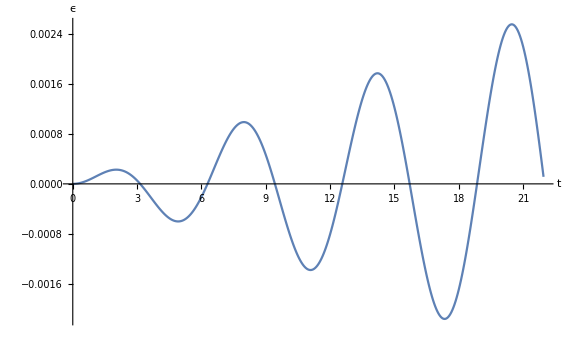

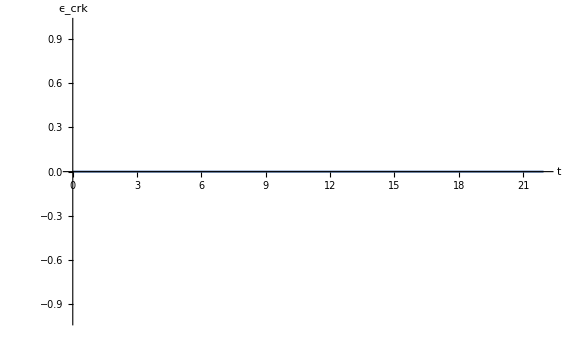

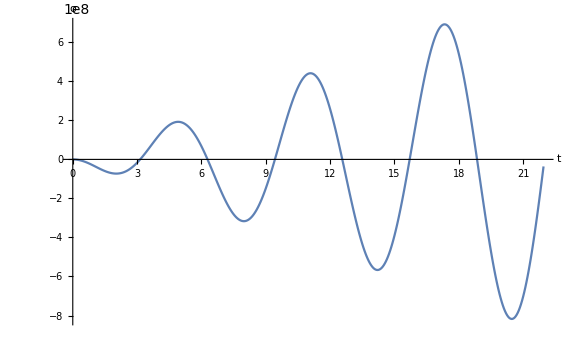

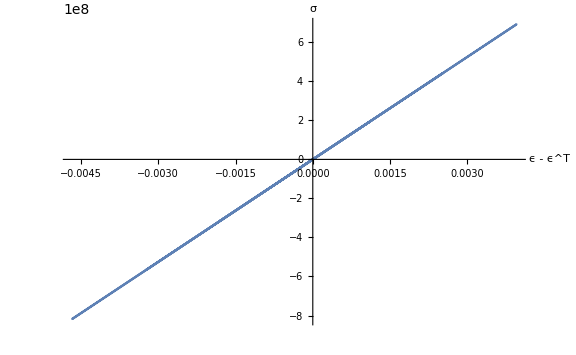

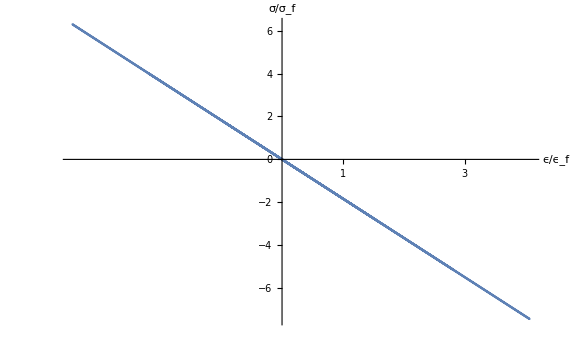

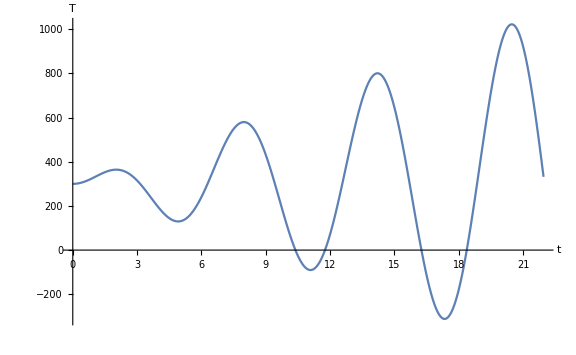

```mathematica
tϵ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 4⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, AxesLabel->{"t", "ϵ"},AxesStyle->Black]
tϵcrk = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, -1⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "ϵ_crk"},AxesStyle->Black]
tσ = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large,  AxesLabel->{"t", "σ"},AxesStyle->Black]
dϵσ = ListPlot[Table[{data⟦i, 2, 5⟧, data⟦i, 2, 3⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"ϵ - ϵ^T", "σ"},AxesStyle->Black]
normdϵσ = ListPlot[Table[{data⟦i, 2, 4⟧/ϵf, data⟦i, 2, 3⟧/σf}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True,ImageSize->Large, Ticks->{Table[i,{i,1,10}], Automatic},AxesLabel->{"ϵ/ϵ_f", "σ/σ_f"},AxesStyle->Black]
tT = ListPlot[Table[{data⟦i, 2, 1⟧, data⟦i, 2, 2⟧}, {i, 1,IntegerPart@ (Subscript[T, f]/Subscript[h, t])}], Joined->True, ImageSize->Large,AxesLabel->{"t", "T"},AxesStyle->Black ]
```

### Сохраняем графики

```mathematica
If[False, 
SetDirectory[NotebookDirectory[]];
options =StringJoin[ToString@TT~StringJoin~"/", StringJoin["h_", ToString[h] ~StringJoin~"_"], StringJoin["tau_", ToString[τ]]];
With[
{directory=FileNameJoin[{ParentDirectory@NotebookDirectory[], StringJoin["LaTeX/pic/",options ]}]},
Switch[FileType[directory],
None,CreateDirectory[directory],
Directory, Print["Overriding files in directory: "~StringJoin~directory]
];
Export[FileNameJoin[{directory, "epsilon(t).pdf"}], tϵ];
Export[FileNameJoin[{directory, "epsilon_crk(t).pdf"}], tϵcrk];
Export[FileNameJoin[{directory, "sigma(t).pdf"}], tσ];
Export[FileNameJoin[{directory, "sigma(epsilon).pdf"}], dϵσ];
Export[FileNameJoin[{directory, "norm_sigma(epsilon).pdf"}], normdϵσ];
Export[FileNameJoin[{directory, "T(t).pdf"}], tT];
]
];
```

```mathematica
Solve[{x == 1, y == 1}, {x, y}]⟦All, 1⟧
```

{x→1}